```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/ethans/GitHub/161/img

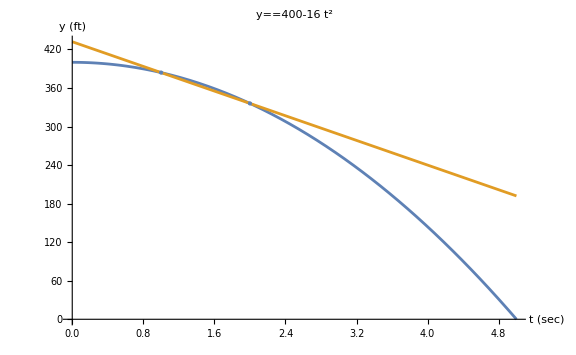

avg_roc1.png

3

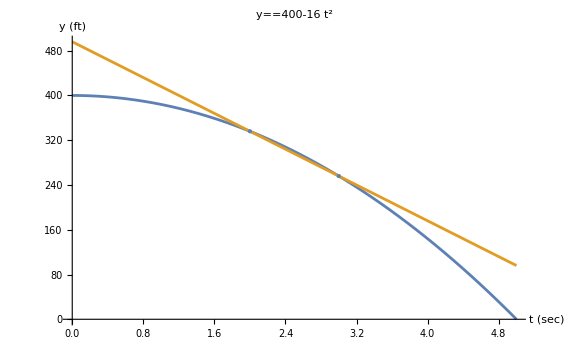

avg_roc2.png

```mathematica
f[t_]=400-16*t^2;
{a,b}={0,5};
c1=1;
c2=2;
m=(f[c2]-f[c1])/(c2-c1);

l[t_]=m*(t-c1)+f[c1]//Expand;
plt1=Show[Plot[{f[t],l[t]},{t,a,b},PlotLabel->y==f[t],AxesLabel->{"t (sec)", "y (ft)"},ImageSize->Large,PlotRange->All],
ListPlot[{{c1,f[c1]},{c2,f[c2]}},PlotStyle->PointSize[Large]]
]
Export["avg_roc1.png",plt1]
c1=2;
c2=3
m=(f[c2]-f[c1])/(c2-c1);
l[t_]=m*(t-c1)+f[c1]//Expand;
plt2=Show[
Plot[{f[t],l[t]},{t,a,b},PlotLabel->y==f[t],AxesLabel->{"t (sec)", "y (ft)"},ImageSize->Large,PlotRange->All],
ListPlot[{{c1,f[c1]},{c2,f[c2]}},PlotStyle->PointSize[Large]]
]
Export["avg_roc2.png",plt2]
```

```mathematica
c=2;
v[h_]=(f[c+h]-f[c])/h;
TableForm[Table[N[{-10^(-n),v[-10^(-n)]},11],{n,0,10}]]
```

-1. | -48.
-0.1 | -62.4
-0.01 | -63.84
-0.001 | -63.984
-0.0001 | -63.9984
-0.00001 | -63.99984
-1.×10^-6 | -63.999984
-1.×10^-7 | -63.9999984
-1.×10^-8 | -63.99999984
-1.×10^-9 | -63.999999984
-1.×10^-10 | -63.999999998

```mathematica
TableForm[Table[N[{10^(-n),v[10^(-n)]},11],{n,0,10}]]
```

1. | -80.
0.1 | -65.6
0.01 | -64.16
0.001 | -64.016
0.0001 | -64.0016
0.00001 | -64.00016
1.×10^-6 | -64.000016
1.×10^-7 | -64.0000016
1.×10^-8 | -64.00000016
1.×10^-9 | -64.000000016
1.×10^-10 | -64.000000002

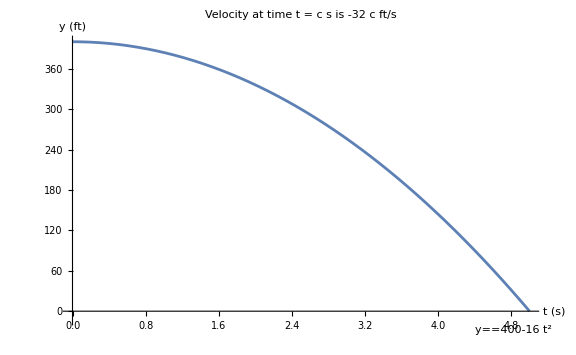

roc.png

```mathematica
m=f'[c];
l[t_]=m*(t-c)+f[c]//Expand;
plt=Show[
Plot[{f[t],l[t]},{t,a,b},PlotLabel->StringForm["Velocity at time t = `` s is `` ft/s",c,m],PlotLabels->Placed[{y==f[t],y==l[t]},Below],AxesLabel->{"t (s)", "y (ft)"},ImageSize->Large,PlotRange->All],
ListPlot[{{c,f[c]}},PlotStyle->PointSize[Large]]
]
Export["roc.png",plt]
```